## Simeck Implementation

```mathematica
(*Define the number of rounds for different block size and key size combinations*)numRounds=<|{32,64}->32,{48,96}->36,{64,128}->44|>;

(*Function to generate the sequence used in key scheduling*)
GetSequence[numRounds_]:=Module[{states,feedback},
(*Initialize states based on number of rounds*)states=If[numRounds<40,ConstantArray[1,5],ConstantArray[1,6]];
(*Generate the sequence*)
Do[
feedback=If[numRounds>=40,BitXor[states[[i+1]],states[[i]]],BitXor[states[[i+2]],states[[i]]]];
AppendTo[states,feedback],
{i,1,numRounds-Length[states]}
];
states];

(*Left rotation function*)
LROT[x_,r_,wordSize_]:=Module[{modulus=2^wordSize},Mod[BitOr[Mod[BitShiftLeft[x,r],modulus],BitShiftRight[x,wordSize-r]],modulus]];

(*Single round function*)
SimeckRound[roundKey_,left_,right_,wordSize_]:=Module[{newLeft,modulus=2^wordSize},newLeft=Mod[BitXor[right,BitXor[BitAnd[left,LROT[left,5,wordSize]],BitXor[LROT[left,1,wordSize],roundKey]]],modulus];
{newLeft,left}];

(*Key scheduling function*)
GenerateRoundKeys[masterKey_,blockSize_,keySize_]:=Module[{wordSize=blockSize/2,states,constant,roundKeys={},numRounds=numRounds[{blockSize,keySize}],sequence},
(*Initialize states from master key*)states=Table[Mod[BitShiftRight[masterKey,i*wordSize],2^wordSize],{i,0,keySize/wordSize-1}];
sequence=GetSequence[numRounds];
constant=2^wordSize-4;
(*Generate round keys*)
Do[
AppendTo[roundKeys,states[[1]]];
{newLeft,newRight}=SimeckRound[BitXor[constant,sequence[[i]]],states[[2]],states[[1]],wordSize];
states=RotateLeft[Append[states,newLeft],1];
states[[1]]=newRight,
{i,1,numRounds}];
roundKeys];

(*Encryption function*)
SimeckEncrypt[plaintext_,roundKeys_,blockSize_]:=Module[{wordSize=blockSize/2,left,right,modulus=2^(blockSize/2)},
(*Split plaintext into left and right halves*)
left=BitShiftRight[plaintext,wordSize];
right=Mod[plaintext,modulus];
(*Apply round function for each round key*)
Do[
{left,right}=SimeckRound[roundKeys[[i]],left,right,wordSize],
{i,1,Length[roundKeys]}];
(*Combine left and right to get ciphertext*)
BitOr[BitShiftLeft[left,wordSize],right]];

(*Decryption function*)
SimeckDecrypt[ciphertext_,roundKeys_,blockSize_]:=Module[{wordSize=blockSize/2,left,right,modulus=2^(blockSize/2)},(*Split ciphertext into left and right halves*)
left=BitShiftRight[ciphertext,wordSize];
right=Mod[ciphertext,modulus];
(*Apply round function in reverse order*)
Do[
{right,left}=SimeckRound[roundKeys[[i]],right,left,wordSize],
{i,Length[roundKeys],1,-1}];
(*Combine left and right to get plaintext*)
BitOr[BitShiftLeft[left,wordSize],right]];

(*Test function*)
TestSimeck[blockSize_,keySize_,masterKey_,plaintext_]:=Module[{roundKeys,ciphertext,decrypted},
(*Generate round keys*)
roundKeys=GenerateRoundKeys[masterKey,blockSize,keySize];
(*Perform encryption*)
ciphertext=SimeckEncrypt[plaintext,roundKeys,blockSize];
(*Perform decryption*)
decrypted=SimeckDecrypt[ciphertext,roundKeys,blockSize];
(*Print results*)
Print["Simeck ",blockSize,"-",keySize];
Print["Key: ",IntegerString[masterKey,16,keySize/4]];
Print["Plaintext: ",IntegerString[plaintext,16,blockSize/4]];
Print["Ciphertext: ",IntegerString[ciphertext,16,blockSize/4]];
Print["Decrypted: ",IntegerString[decrypted,16,blockSize/4]];
Print[];
{ciphertext,decrypted}
];

(*Example usage*)
(*Test vectors from the Python implementation*)
plaintext32=FromDigits["65656877",16];
key64=FromDigits["1918111009080100",16];
TestSimeck[32,64,key64,plaintext32];

plaintext48=FromDigits["72696320646e",16];
key96=FromDigits["1a19181211100a0908020100",16];
TestSimeck[48,96,key96,plaintext48];

plaintext64=FromDigits["656b696c20646e75",16];
key128=FromDigits["1b1a1918131211100b0a090803020100",16];
TestSimeck[64,128,key128,plaintext64];
```

Simeck 32-64

Key: 1918111009080100

Plaintext: 65656877

Ciphertext: 34a56b8c

Decrypted: 65656877

Simeck 48-96

Key: 1a19181211100a0908020100

Plaintext: 72696320646e

Ciphertext: 22b097524033

Decrypted: 72696320646e

Simeck 64-128

Key: 1b1a1918131211100b0a090803020100

Plaintext: 656b696c20646e75

Ciphertext: 01a3c0a262206351

Decrypted: 656b696c20646e75

## Benchmarking

```mathematica
(*Benchmarking function for Simeck cipher*)BenchmarkSimeck[blockSize_,keySize_,numIterations_:100]:=Module[{masterKey,plaintext,roundKeys,times,memoryBefore,memoryAfter,averageTime,memoryUsage,results},(*Test configuration*)masterKey=Switch[keySize,64,FromDigits["1918111009080100",16],96,FromDigits["1a19181211100a0908020100",16],128,FromDigits["1b1a1918131211100b0a090803020100",16]];
plaintext=Switch[blockSize,32,FromDigits["65656877",16],48,FromDigits["72696320646e",16],64,FromDigits["656b696c20646e75",16]];
(*Generate round keys once before benchmarking*)
roundKeys=GenerateRoundKeys[masterKey,blockSize,keySize];
(*Measure encryption speed*)
Print["Starting encryption speed test..."];
times=Table[First[AbsoluteTiming[SimeckEncrypt[plaintext,roundKeys,blockSize];]],{numIterations}];
averageTime=Mean[times];
(*Measure memory usage*)
Print["Starting memory usage test..."];
memoryBefore=MemoryInUse[];
SimeckEncrypt[plaintext,roundKeys,blockSize];
memoryAfter=MemoryInUse[];
memoryUsage=memoryAfter-memoryBefore;
(*Collect and format results*)results={"Configuration"->{"Block Size"->blockSize,"Key Size"->keySize,"Number of Iterations"->numIterations},"Performance"->{"Average Time per Encryption"->averageTime,"Encryptions per Second"->N[1/averageTime],"Memory Usage (bytes)"->memoryUsage},"Statistics"->{"Min Time"->Min[times],"Max Time"->Max[times],"Standard Deviation"->StandardDeviation[times]}};
(*Print formatted results*)
Print[Style["Simeck ",Bold],blockSize,"-",keySize," Benchmark Results:"];
Print[Style["Configuration:",Bold]];
Print["  Block Size: ",blockSize," bits"];
Print["  Key Size: ",keySize," bits"];
Print["  Number of Iterations: ",numIterations];
Print[];
Print[Style["Performance Metrics:",Bold]];
Print["  Average Time per Encryption: ",NumberForm[averageTime,{6,6}]," seconds"];
Print["  Encryptions per Second: ",NumberForm[N[1/averageTime],{6,2}]];
Print["  Memory Usage: ",NumberForm[N[memoryUsage/1024],{6,2}]," KB"];
Print[];
Print[Style["Detailed Statistics:",Bold]];
Print["  Minimum Time: ",NumberForm[Min[times],{6,6}]," seconds"];
Print["  Maximum Time: ",NumberForm[Max[times],{6,6}]," seconds"];
Print["  Standard Deviation: ",NumberForm[StandardDeviation[times],{6,6}]," seconds"];
(*Return results as an association for programmatic use*)
<|"Results"->results,"RawTimes"->times|>];

(*Function to compare different configurations*)
CompareSimeckConfigurations[]:=Module[{configurations,results,plotData},configurations={{32,64},{48,96},{64,128}};
results=Table[BenchmarkSimeck[config[[1]],config[[2]]],{config,configurations}];
(*Create labels*)plotLabels=Table[ToString[configurations[[i,1]]]<>"/"<>ToString[configurations[[i,2]]],{i,Length[configurations]}];
(*Create the box plot *)plotData=BoxWhiskerChart[Table[results[[i]]["RawTimes"],{i,Length[results]}],ChartLabels->plotLabels,Frame->True,FrameLabel->{"Configuration (Block Size/Key Size)","Time (seconds)"},ImageSize->500];
(*Return both the plot and numerical results*)
<|"Plot"->plotData,"Results"->results,"RawData"->Table[results[[i]]["RawTimes"],{i,Length[results]}]|>];
```

Running individual benchmark for Simeck-64/128...

Starting encryption speed test...

Starting memory usage test...

Simeck 64-128 Benchmark Results:

Configuration:

Block Size: 64 bits

Key Size: 128 bits

Number of Iterations: 100

Performance Metrics:

Average Time per Encryption: 0.000759 seconds

Encryptions per Second: 1317.42

Memory Usage: 0.03 KB

Detailed Statistics:

Minimum Time: 0.000723 seconds

Maximum Time: 0.001715 seconds

Standard Deviation: 0.000126 seconds

Running comparison across all configurations...

Starting encryption speed test...

Starting memory usage test...

Simeck 32-64 Benchmark Results:

Configuration:

Block Size: 32 bits

Key Size: 64 bits

Number of Iterations: 100

Performance Metrics:

Average Time per Encryption: 0.000570 seconds

Encryptions per Second: 1755.13

Memory Usage: 0.03 KB

Detailed Statistics:

Minimum Time: 0.000530 seconds

Maximum Time: 0.001097 seconds

Standard Deviation: 0.000098 seconds

Starting encryption speed test...

Starting memory usage test...

Simeck 48-96 Benchmark Results:

Configuration:

Block Size: 48 bits

Key Size: 96 bits

Number of Iterations: 100

Performance Metrics:

Average Time per Encryption: 0.000617 seconds

Encryptions per Second: 1620.38

Memory Usage: 0.03 KB

Detailed Statistics:

Minimum Time: 0.000593 seconds

Maximum Time: 0.000777 seconds

Standard Deviation: 0.000030 seconds

Starting encryption speed test...

Starting memory usage test...

Simeck 64-128 Benchmark Results:

Configuration:

Block Size: 64 bits

Key Size: 128 bits

Number of Iterations: 100

Performance Metrics:

Average Time per Encryption: 0.000743 seconds

Encryptions per Second: 1345.59

Memory Usage: 0.03 KB

Detailed Statistics:

Minimum Time: 0.000717 seconds

Maximum Time: 0.000807 seconds

Standard Deviation: 0.000019 seconds

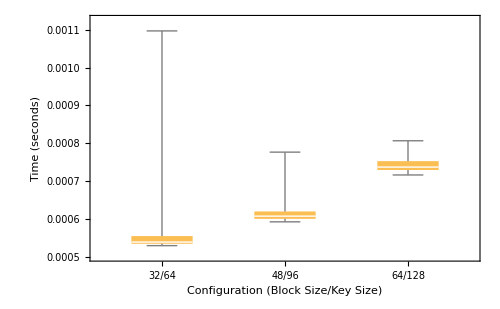

```mathematica
(*Example usage*)
Module[{benchmarkResults},
(*Run individual benchmark*)
Print[Style["Running individual benchmark for Simeck-64/128...",Bold]];
BenchmarkSimeck[64,128];
(*Run comparison and display results*)
Print[Style["\nRunning comparison across all configurations...",Bold]];
benchmarkResults=CompareSimeckConfigurations[];
(*Display the plot*)
benchmarkResults["Plot"]
]
```